```mathematica
(* Defects with the symmetry along <100> direction *)
```

```mathematica
d100 = {1, 0, 0}; d010 = {0, 1, 0}; d001 = {0, 0, 1};
```

```mathematica
(* Defects with the symmetry along <110> direction *)
d110 = 1/√2*{1, 1, 0}; d101 = 1/√2*{1, 0, 1};
d011 = 1/√2*{0, 1, 1}; d1m10 = 1/√2*{1, -1, 0}; d01m1 = 1/√2*{0, 1, -1}; d10m1 = 1/√2*{1, 0, -1};
```

```mathematica
(* Defects with the symmetry along <111> direction *)
d111 = 1/√3*{1, 1, 1}; dm1m11 = 1/√3*{-1, -1, 1};
d1m1m1 = 1/√3*{1, -1, -1}; dm11m1 = 1/√3*{-1, 1, -1};
```

```mathematica
(* Rotation of the vector "d" in the XY plane by the angle theta "th" *)
Rot[d_, th_] := {d[[1]]*Cos[Pi*th/180]-d[[2]]*Sin[Pi*th/180], d[[1]]*Sin[Pi*th/180]+d[[2]]*Cos[Pi*th/180], d[[3]]};
```

```mathematica
(* Project vector b on a: Return part of b that is parallel to a *)
ParA[a_, b_] := a*(a.b)/Norm[a]^2;
(* Project vector b perpendicular to a: Return part of b that is orthogonal to a *)
PerpA[a_, b_] := b - ParA[a, b];
```

```mathematica
(* Orientations of the analyzer and laser field: co and cross*)
A = {0, 1, 0}; Lco = {0, 1, 0}; Lcr = {1, 0, 0};
(* Direction of observation, along z axis *)
n = {0, 0, 1};
```

```mathematica
(* NO Saturation: linear response*)
Lin[g_] := g;
```

```mathematica
(* YES Saturation with Gaussian beam *)
Sat[g_] := Log[1+g];
```

```mathematica
(* Determines which absorption function (linear L or saturated S) to use *)
absF[x_, sat_] := If[sat=="L", Lin[x], If[sat=="S", Sat[x], 0]];
```

```mathematica
(* Effective absorption amplitude. We consider only electric dipole absorption *)
```

```mathematica
Pabs[d_, L_, mAbs_, g_, sat_, th_] := If[mAbs=="z", absF[g*Norm[ParA[Rot[d, th], L]]^2, sat],If[mAbs=="xy",  absF[g*Norm[PerpA[Rot[d, th], L]]^2, sat], 0]];
```

```mathematica
PabsB[d_, L_, mAbs_, g_, sat_, th_, B_] := If[mAbs=="z", absF[g*Norm[ParA[Rot[d, th], L]]^2*(1-B)+B, sat],If[mAbs=="xy",  absF[g*Norm[PerpA[Rot[d, th], L]]^2+B*g*Norm[ParA[Rot[d, th], L]]^2*(1-B)+B, sat], 0]];
```

```mathematica
(* Electric Dipole Z-type emission. Aperture Accounted for *)
```

```mathematica
Iz[d_, xM_] := 1/960 π (128 (d[[1]]^2+8 d[[2]]^2+d[[3]]^2)-30 (5d[[1]]^2+31 d[[2]]^2+4d[[3]]^2) Cos[xM]+5 (5 d[[1]]^2-17 d[[2]]^2-4d[[3]]^2) Cos[3 xM]-3 (d[[1]]^2+3 d[[2]]^2-4 d[[3]]^2) Cos[5 xM]);
```

```mathematica
(* Electric Dipole XY-type emission. Aperture Accounted for*)
```

```mathematica
Ixy[d_, xM_] := -1/12 π (-16+15 Cos[xM]+Cos[3 xM])-1/960 π (128 (d[[1]]^2+8 d[[2]]^2+d[[3]]^2)-30 (5d[[1]]^2+31 d[[2]]^2+4d[[3]]^2) Cos[xM]+5 (5 d[[1]]^2-17 d[[2]]^2-4d[[3]]^2) Cos[3 xM]-3 (d[[1]]^2+3 d[[2]]^2-4 d[[3]]^2) Cos[5 xM]);
```

```mathematica
(* Effective emission amplitude. We consider two cases: *)
(* E -- electric dipole and M -- magnetic dipole *)
(* For either of them dipole (p or m) can be parallel ("z") or *)
(* or perpendicular ("xy") to the defect vector *)
(* Electric dipole emission function *)
PEem[n_, d_, A_,  mEm_, th_] := If[mEm=="z", Norm[ParA[Rot[d, th], PerpA[n, A]]]^2, If[mEm=="xy",Norm[PerpA[Rot[d, th], PerpA[n, A]]]^2,0]];
PEemB[n_, d_, A_,  mEm_, th_, B_] := If[mEm=="z", Norm[ParA[Rot[d, th], PerpA[n, A]]]^2*(1-B)+B, If[mEm=="xy",Norm[PerpA[Rot[d, th], PerpA[n, A]]]^2*(1-B)+B,0]];
PEemAp[d_, mEm_, th_, xM_] := If[mEm=="z", Iz[Rot[d, th], xM], If[mEm=="xy",Ixy[Rot[d, th], xM],0]];
PMem[n_, d_, A_,  mEm_, th_] := If[mEm=="z", Norm[ParA[Rot[d, th], Cross[n, A]]]^2, If[mEm=="xy",Norm[PerpA[Rot[d, th], Cross[n, A]]]^2,0]];
```

```mathematica
(*P[n_, d_, A_, L_, mAbs_, mEm_, g_, sat_, th_] := Pabs[d, L, mAbs, g, sat, th]*PEem[n, d, A, mEm, th];*)
```

```mathematica
P[n_, d_, A_, L_, mAbs_, mEm_, g_, sat_, th_] := Pabs[d, L, mAbs, g, sat, th]*PEemAp[d,  mEm, th];
PB[n_, d_, A_, L_, mAbs_, mEm_, g_, sat_, th_, B_] := PabsB[d, L, mAbs, g, sat, th, B]*PEemB[n, d,  A, mEm, th, B];
```

```mathematica
P100[A_, L_, mAbs_, mEm_, g_, sat_, th_, B_] := PB[n, d100, A, L, mAbs, mEm, g, sat, th, B]+PB[n, d010, A, L, mAbs, mEm, g, sat, th, B]+PB[n, d001, A, L, mAbs, mEm, g, sat, th, B]
```

```mathematica
P110[A_, L_, mAbs_, mEm_, g_, sat_, th_, B_] := PB[n, d110, A, L, mAbs, mEm, g, sat, th, B]+PB[n, d101, A, L, mAbs, mEm, g, sat, th, B]+PB[n,d011, A, L, mAbs, mEm, g, sat, th, B]+PB[n, d1m10, A, L, mAbs, mEm, g, sat, th, B]+PB[n, d01m1, A, L, mAbs, mEm, g, sat, th, B]+PB[n,d10m1, A, L, mAbs, mEm, g, sat, th, B]
```

```mathematica
P111[A_, L_, mAbs_, mEm_, g_, sat_, th_, B_] := PB[n,d111, A, L, mAbs, mEm, g, sat, th, B]+PB[n, dm1m11, A, L, mAbs, mEm, g, sat, th, B]+PB[n,d1m1m1, A, L, mAbs, mEm, g, sat, th, B]+PB[n,dm11m1, A, L, mAbs, mEm, g, sat, th, B]
```

```mathematica
Manipulate[Show[PolarPlot[P111[A, Lcr, "z", "xy", s, "L",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}], PolarPlot[P111[A, Lcr, "z", "xy", s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}], PolarPlot[P111[A, Lcr, "xy", "z", s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}]], {s, 10, 50}, {B, 0.0, 1.0}]
```

```mathematica
Pol100[mAbs_, mEm_, g_, sat_, th_, B_] :=( P100[A, Lco, mAbs, mEm, g, sat, th, B] - P100[A, Lcr, mAbs, mEm, g, sat, th, B] )/ ( P100[A, Lco, mAbs, mEm, g, sat, th, B] + P100[A, Lcr, mAbs, mEm, g, sat, th, B] );
```

```mathematica
Pol110[mAbs_, mEm_, g_, sat_, th_, B_] :=( P110[A, Lco, mAbs, mEm, g, sat, th, B] - P110[A, Lcr, mAbs, mEm, g, sat, th, B] )/ ( P110[A, Lco, mAbs, mEm, g, sat, th, B] + P110[A, Lcr, mAbs, mEm, g, sat, th, B] );
```

```mathematica
Pol111[mAbs_, mEm_, g_, sat_, th_, B_] :=( P111[A, Lco, mAbs, mEm, g, sat, th, B] - P111[A, Lcr, mAbs, mEm, g, sat, th, B] )/ ( P111[A, Lco, mAbs, mEm, g, sat, th, B] + P111[A, Lcr, mAbs, mEm, g, sat, th, B] );
```

```mathematica
Manipulate[Show[PolarPlot[Pol100["z", "z", s, "L",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}], PolarPlot[Pol100["z", "z", s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}], PolarPlot[Pol100["z", "z", s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}]], {s, 0.1, 50}, {B, 0.0, 1.0}]
```

```mathematica
Manipulate[Show[Plot[Pol111["z", "z", s, "L",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}], Plot[Pol111["z", "z", s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}], Plot[Pol111["z", "z", s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}]], {s, 0.1, 50}, {B, 0.0, 1.0}]
```

```mathematica
PlotSatPol100[abs_, em_, B_] := Show[Plot[Pol100[abs, em, 10.0, "L",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}, PlotRange->All], Plot[Pol100[abs, em, 10.0, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}, PlotRange->All], Plot[Pol100[em, abs, 10.0, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Green, Thick, PlotRange->All}]];
```

```mathematica
PlotSatPol110[abs_, em_, s_, B_] := Show[Plot[Pol110[abs, em, s, "L",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}, PlotRange->All], Plot[Pol110[abs, em, s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}, PlotRange->All], Plot[Pol110[em, abs, s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}, PlotRange->All]];
```

```mathematica
PlotSatPol111[abs_, em_, s_, B_] := Show[Plot[Pol111[abs, em, s, "L",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}, PlotRange->All], Plot[Pol111[abs, em, s, "S",180*x/Pi, B], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}, PlotRange->All], Plot[Pol111[em, abs, s, "S",180*x/Pi,B], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}, PlotRange->All]];
```

```mathematica
PlotSatPol100["z", "xy", 8.0, 0.0]
```

PlotSatPol100[z,xy,8.,0.]

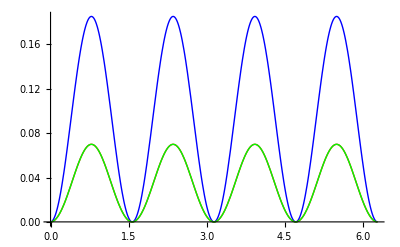

```mathematica
PlotSatPol111["xy", "xy", 20, 0.1]
```

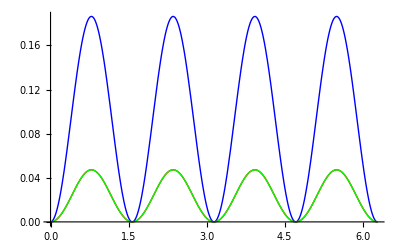

```mathematica
PlotSatPol111["xy", "xy", 100, 0.1]
```

```mathematica
Manipulate[ Show[Plot[Pol100["z", "z", 10.0, "L",180*th/Pi, B]/Pol100["z", "z", 10.0, "L",180*th/Pi, 0], {B, 0.0, 1.0}, PlotRange->Full], Plot[Pol110["z", "z", 10.0, "L",180*th/Pi, B]/Pol110["z", "z", 10.0, "L",180*th/Pi, 0], {B, 0.0, 1.0}, PlotRange->Full]], {th, 0, 90}]
```

```mathematica
Manipulate[Plot[Pol111["z", "z", 0.1, "L",180*th/Pi, B]/Pol111["z", "z", 0.1, "L",180*th/Pi, 0], {B, 0.0, 1.0}, PlotRange->Full], {th, 0.1, 90}]
```

```mathematica
H[b_] := (1-b)^2/( (1+b)^2+2*b^2);
```

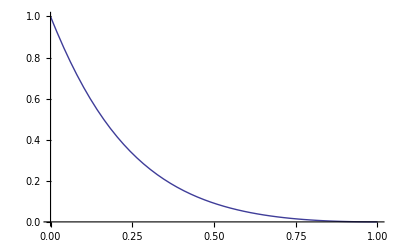

```mathematica
Plot[H[b], {b, 0, 1}]
```

```mathematica
Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, B]]]]/Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, 0]]]]
```

((0.707107-0.707107 B)^2 (1+Cos[4 th]))/((1.+B (2.+3. B)) (0.5+0.5 Cos[4 th]))

```mathematica
FullSimplify[Expand[Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, B]]]]/Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, 0]]]]]]
```

(1.-1. B)^2/(1.+B (2.+3. B))

```mathematica
FullSimplify[Expand[Assuming[th >0  && B > 0, FullSimplify[Expand[Pol110["z", "z", 1.0, "L",180*th/Pi, B]]]]/Assuming[th >0 , FullSimplify[Expand[Pol110["z", "z", 1.0, "L",180*th/Pi, 0]]]]]]
```

(((0.866025+0. ⅈ)-(0.866025+0. ⅈ) B)^2+((0.+0.5 ⅈ)-(0.+0.5 ⅈ) B)^2 Cos[4 th])/(((1.5+0. ⅈ)+B ((5.+0. ⅈ)+(5.5+0. ⅈ) B)) ((0.5+0. ⅈ)-(2.82773×10^-17+0. ⅈ) Cos[2 th]-(0.166667+0. ⅈ) Cos[4 th]-(1.19262×10^-18+0. ⅈ) Cos[8 th]+(0.+2.77556×10^-17 ⅈ) Cos[th] Sin[th]))

```mathematica
(0.5-0.16666666666666669Cos[4 th])
```

0.5-0.166667 Cos[4 th]

```mathematica
(1.5+B (5+5.5 B))
```

1.5+B (5+5.5 B)

```mathematica
FullSimplify[Expand[Assuming[th >0  && B > 0, FullSimplify[Expand[Pol111["z", "z", 1.0, "L",180*th/Pi, B]]]]]]
```

$Aborted

```mathematica
FullSimplify[Expand[Assuming[th >0 , FullSimplify[Expand[Pol100["xy", "xy", 1.0, "L",180*th/Pi, B]]]]/Assuming[th >0 , FullSimplify[Expand[Pol100["xy", "xy", 1.0, "L",180*th/Pi, 0]]]]]]
```

((-1.44225+1.44225 B) ((-0.721125-1.24902 ⅈ)+1.44225 B) ((-0.721125+1.24902 ⅈ)+1.44225 B))/(-3.+B (-6.+B (-2.+1. B)))

```mathematica
Expand[(-1.4422495703074083+1.4422495703074083 B) ((-0.7211247851537042-1.2490247664834064 ⅈ)+1.4422495703074083 B) ((-0.7211247851537042+1.2490247664834064 ⅈ)+1.4422495703074083 B)]
```

(-3.+1.55908×10^-16 ⅈ)+(6.-4.44089×10^-16 ⅈ) B-(6.-4.44089×10^-16 ⅈ) B^2+3. B^3